```mathematica
xdata={-15,-11,-7,-3,1,5,9,13,17,21,25,29,33,37,41};
ydata={0.47,0.54,0.79,1.32,1.13,1.26,3.02,2.99,3.15,3.90,5.04,7.72,11.02,13.42,20.85};
```

```mathematica
(*xdata={-15,-11,-7,-3,1,5,9,13,17,21,25,29,33,37,41};
ydata={0.69,0.78,1.14,1.92,1.64,1.83,4.38,4.34,4.57,5.66,7.31,11.19,15.99,19.46,30.24};*)
```

```mathematica
Grid[Transpose[{xdata,ydata}]]
```

-15 | 0.47
-11 | 0.54
-7 | 0.79
-3 | 1.32
1 | 1.13
5 | 1.26
9 | 3.02
13 | 2.99
17 | 3.15
21 | 3.9
25 | 5.04
29 | 7.72
33 | 11.02
37 | 13.42
41 | 20.85

```mathematica
Grid[Transpose[{xdata,ydata}]]//TeXForm//CopyToClipboard
```

```mathematica
xbar=Mean[xdata]
ybar=Mean[ydata]
```

13

5.108

```mathematica
n=Length[xdata]
```

15

```mathematica
σTρ=Sum[(xdata[[i]]-xbar)(ydata[[i]]-ybar),{i,1,Length[xdata]}]/Length[xdata]
```

83.688

```mathematica
σT=Sqrt[Sum[(xdata[[i]]-xbar)^2,{i,1,Length[xdata]}]/Length[xdata]]//N
```

17.282

```mathematica
σρ=Sqrt[Sum[(ydata[[i]]-ybar)^2,{i,1,Length[xdata]}]/Length[xdata]]//N
```

5.6499

```mathematica
σTρ/(σT σρ)
```

0.857095

```mathematica
LinearModelFit[Transpose[{xdata,ydata}],x,x]["RSquared"]//Sqrt
```

0.857095

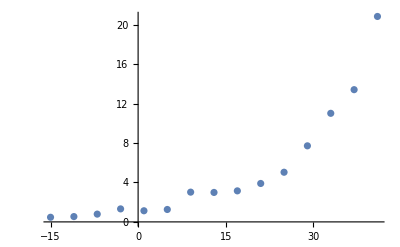

```mathematica
ListPlot[Transpose[{xdata,ydata}]]
```

## Regression

```mathematica
sumx=Total[xdata]
sumy=Total[ydata]
sumx2=Total[#^2&/@xdata]
sumxy=Sum[xdata[[i]]*ydata[[i]],{i,1,Length[xdata]}]
```

195

76.62

7015

2251.38

```mathematica
Δ=n sumx2 - (sumx)^2
```

67200

```mathematica
a=1/Δ(sumx2 sumy - sumx sumxy)
```

1.46533

```mathematica
b=1/Δ(n sumxy -sumx sumy)
```

0.280205

```mathematica
NumberForm[0.2802053571428572,16]
```

0.2802053571428572

```mathematica
NumberForm[1.4653303571428555,16]//CopyToClipboard
```

```mathematica
fit=LinearModelFit[Transpose[{xdata,ydata}],x,x]
```

FittedModel[1.46533+0.280205 x]

### Errors

```mathematica
s2=(∑_(i=1)^Length[ydata] (ydata⟦i⟧-a-b xdata⟦i⟧)^2)/(n-2)
```

9.77488

```mathematica
√((s2 sumx2)/Δ)
```

1.01015

```mathematica
Sqrt[n s2/Δ]
```

0.0467107

## Plotting

```mathematica
cross=Graphics[{Line[{{-1,-1},{1,1}}],Line[{{1,-1},{-1,1}}]},ImageSize->11,ImagePadding->1.5]
```

-Graphics-

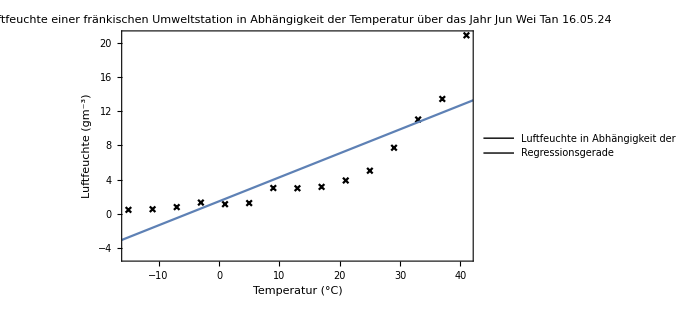

```mathematica
plt=Legended[Show[ListPlot[Transpose[{xdata,ydata}],PlotMarkers->{cross,0.02},PlotStyle->Black],Plot[fit[x],{x,Min[xdata]-100,Max[xdata]+100}],PlotRange->{{Min[xdata],Max[xdata]},{-5,Max[ydata]}},Frame->True,Axes->False,FrameStyle->Thickness[0.003],FrameTicksStyle->Directive[15,Black,Opacity[1],FontOpacity[1]],ImageSize->500,PlotLegends->Automatic,FrameLabel->{"Temperatur (°C)","Luftfeuchte (gm^-3)"},LabelStyle->Directive[Black,15],PlotLabel->"Luftfeuchte einer fränkischen Umweltstation in\nAbhängigkeit der Temperatur über das Jahr\n Jun Wei Tan 16.05.24"],Placed[SwatchLegend[{Black,ColorData[97,1]},{TextCell["Luftfeuchte in\nAbhängigkeit der Temperatur"],"Regressionsgerade"},LegendMarkers->{cross,Graphics[{Line[{{0,0},{1,0}}]}]}],{Scaled[0.20],Scaled[0.88]}]]
```

```mathematica
Export[NotebookDirectory[]<>"plt.pdf",plt,Background->None]
```

D:\Documents\GitHub\Uni-Wuerzburg-Bachlor-MathPhy\Ubungen\Advanced Mistake Counting\plt.pdf